## Funciones dieléctricas de eritrocitos

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Importación de paquetes

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["KramersKronig`"]
Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
Needs["LorentzFitSSKK`"]
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

tolRes0=1.*^-8;
```

## Funciones generales

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
eps[parteRe_,parteIm_,x_]:=(parteRe[x]+I parteIm[x])^2;
```

## Datos beta y H2O -> Parte real

```mathematica
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]]
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];

(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

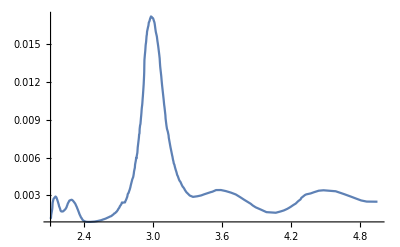

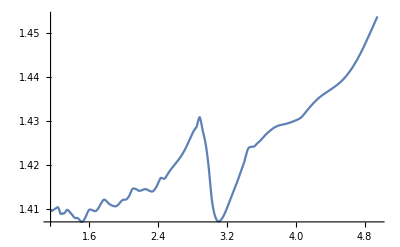

```mathematica
datosuA30=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm300=Transpose[{datos1uA30[[All,1]],datos3im30}];
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe30[x_]:=parteRe[x,30.6]

Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe30[x],{x,1.15,4.95},PlotRange->All]
```

```mathematica
(*Función dieléctrica experimental*)
eps30Im[x_]:=Im[eps[parteRe30,parteIm30,x]];
eps30Re[x_]:=Re[eps[parteRe30,parteIm30,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos30={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
ajusteSinPico[eps30Im,intervalos30,1.*^-8,xmin30,xmax30];
```

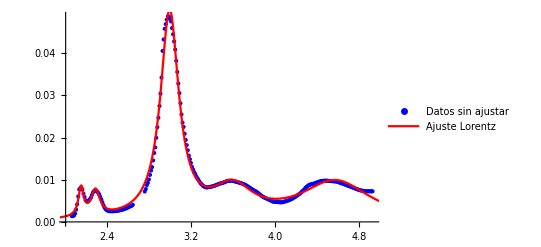

```mathematica
Show[ListPlot[ajusteSinPico[eps30Im,intervalos30,1.*^-8,xmin30,xmax30][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajusteSinPico[eps30Im,intervalos30,1.*^-8,xmin30,xmax30][[2]][ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

```mathematica
ajustePico[eps30Im];
```

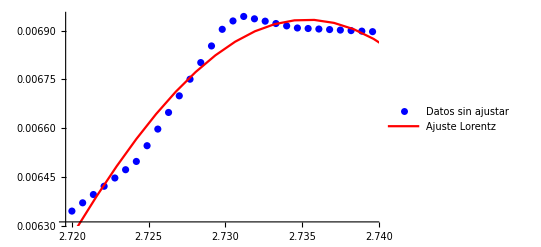

```mathematica
Show[ListPlot[ajustePico[eps30Im][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajustePico[eps30Im][[2]][ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

```mathematica
ajusteTotal[eps30Im,intervalos30,1.*^-8,xmin30,xmax30];
```

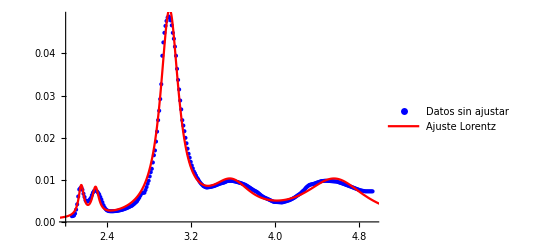

```mathematica
Show[ListPlot[ajusteTotal[eps30Im,intervalos30,1.*^-8,xmin30,xmax30][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajusteTotal[eps30Im,intervalos30,1.*^-8,xmin30,xmax30][[2]][ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

## Concentración 28.7 g/dL

### Importación de datos

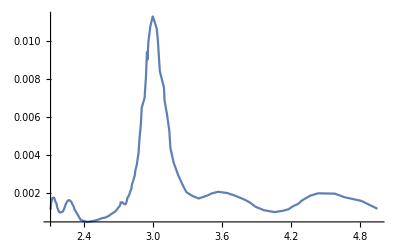

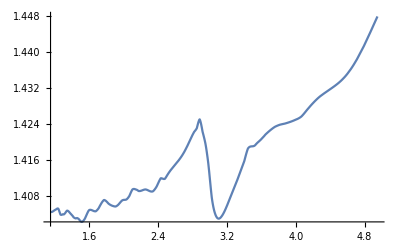

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];

parteRe28[x_]:=parteRe[x,28.7];

Plot[parteIm28[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe28[x],{x,1.15,4.95},PlotRange->All]
```

### Ajuste de lorentzianas

```mathematica
(*Función dieléctrica experimental*)
eps28Im[x_]:=Im[eps[parteRe28,parteIm28,x]];
eps28Re[x_]:=Re[eps[parteRe28,parteIm28,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
{xmin28,xmax28}={Min[datos2Im],Max[datos2Im]};
```

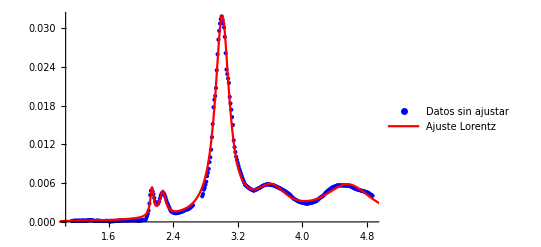

```mathematica
hola=ajusteSinPico[eps28Im,intervalos28,1.*^-8,xmin28,xmax28][[3]];
Show[ListPlot[ajusteSinPico[eps28Im,intervalos28,1.*^-8,xmin28,xmax28][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajusteSinPico[eps28Im,intervalos28,1.*^-8,xmin28,xmax28][[2]][ω],{ω,xmin28-0.5,xmax28+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

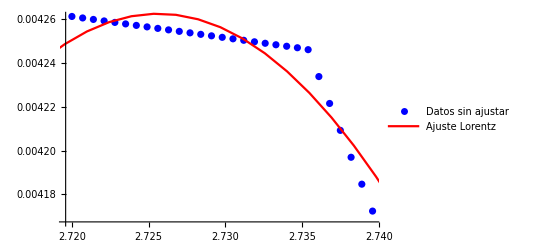

```mathematica
hola1=ajustePico[eps28Im][[3]];
Show[ListPlot[ajustePico[eps28Im][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajustePico[eps28Im][[2]][ω],{ω,xmin28-0.5,xmax28+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```

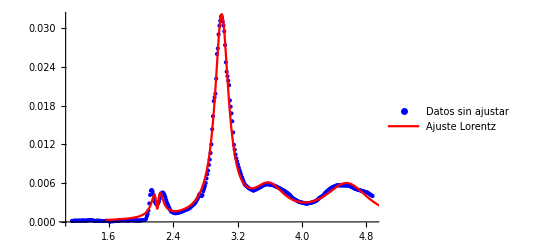

```mathematica
ajusteTotal[eps28Im,intervalos28,1.*^-8,xmin28,xmax28,hola,hola1];


Show[ListPlot[ajusteTotal[eps28Im,intervalos28,1.*^-8,xmin28,xmax28,hola,hola1][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[ajusteTotal[eps28Im,intervalos28,1.*^-8,xmin28,xmax28,hola,hola1][[2]][ω],{ω,xmin30-0.5,xmax30+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
```